```mathematica
degreeDistributionLogBinPlotN250[mode_,g_,nbin_]:=Module[{degdata,degreeseq,h,degreedist},degdata=Import[ToString[StringForm["./Desktop/simulación/MUTACIONES/N250/solve/run1_k4/deg_``.dat",g]],"Table"];
Switch[mode,"In",degreeseq=degdata[[All,3]],"Out",degreeseq=degdata[[All,2]],"Total",degreeseq=degdata[[All,2]]+degdata[[All,3]]];
h=HistogramList[degreeseq,{"Log",nbin}];
degreedist=Table[{(h[[1,i]]+h[[1,i+1]])/2,h[[2,i]]/((h[[1,i+1]]-h[[1,i]]))},{i,1,Length[h[[2]]]}];
ListLogLogPlot[degreedist,PlotRange->{{10^0,10^3},{10^-3,10^4}}(*,PlotLabel->ToString[StringForm["`` degree distribution at g=``",mode,g]]*),FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,5}],None},{Table[{10^i,Superscript[10,i]},{i,-5,5}],None}},Frame->True,PlotMarkers->"OpenMarkers"]]
```

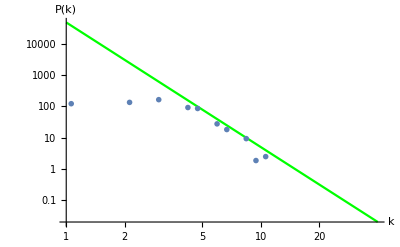

```mathematica
Show[LogLogPlot[50000x^{-4},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["In",0,15]]
```

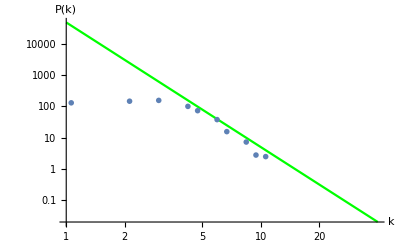

```mathematica
Show[LogLogPlot[50000x^{-4},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["Out",0,15]]
```

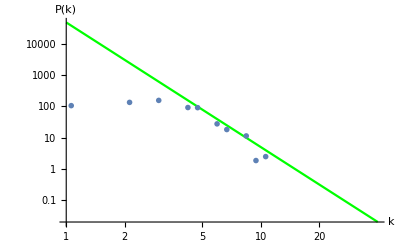

```mathematica
Show[LogLogPlot[50000x^{-4},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["In",20,15]]
```

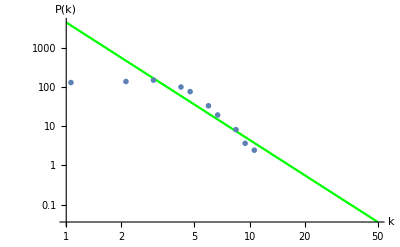

```mathematica
Show[LogLogPlot[4500x^{-3},{x,1,50},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["Out",20,15]]
```

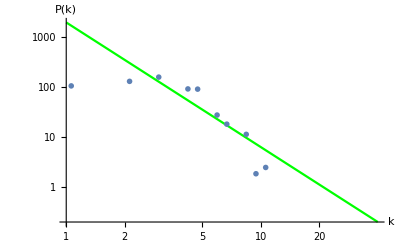

```mathematica
Show[LogLogPlot[2000x^{-2.5},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["In",21,15]]
```

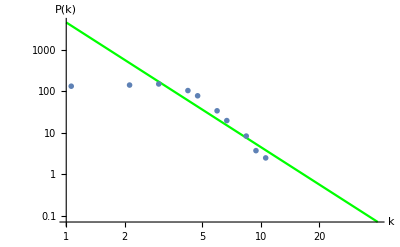

```mathematica
Show[LogLogPlot[4500x^{-3},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN250["Out",21,15]]
```

```mathematica
degreeDistributionLogBinPlotN500[mode_,g_,nbin_]:=Module[{degdata,degreeseq,h,degreedist},degdata=Import[ToString[StringForm["./Desktop/simulación/MUTACIONES/N500/r1/solve_nutytrans75/deg_``.dat",g]],"Table"];
Switch[mode,"In",degreeseq=degdata[[All,3]],"Out",degreeseq=degdata[[All,2]],"Total",degreeseq=degdata[[All,2]]+degdata[[All,3]]];
h=HistogramList[degreeseq,{"Log",nbin}];
degreedist=Table[{(h[[1,i]]+h[[1,i+1]])/2,h[[2,i]]/((h[[1,i+1]]-h[[1,i]]))},{i,1,Length[h[[2]]]}];
ListLogLogPlot[degreedist,PlotRange->{{10^0,10^3},{10^-3,10^4}}(*,PlotLabel->ToString[StringForm["`` degree distribution at g=``",mode,g]]*),FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,5}],None},{Table[{10^i,Superscript[10,i]},{i,-5,5}],None}},Frame->True,PlotMarkers->"OpenMarkers"]]
```

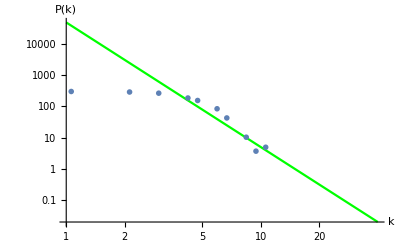

```mathematica
Show[LogLogPlot[50000x^{-4},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["In",0,15]]
```

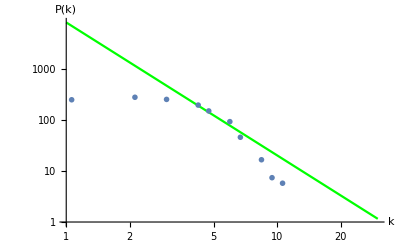

```mathematica
Show[LogLogPlot[8000x^{-2.6},{x,1,30},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["In",100,15]]
```

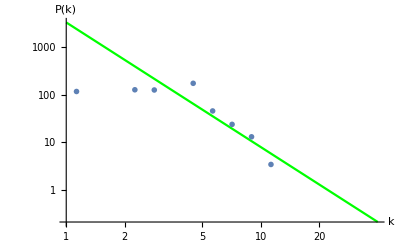

```mathematica
Show[LogLogPlot[3200x^{-2.6},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["In",150,15]]
```

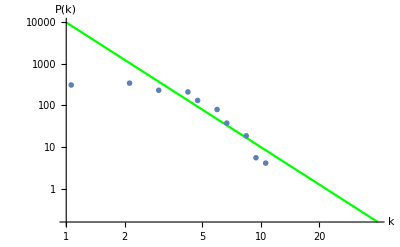

```mathematica
Show[LogLogPlot[10000x^{-3},{x,1,40},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["Out",0,15]]
```

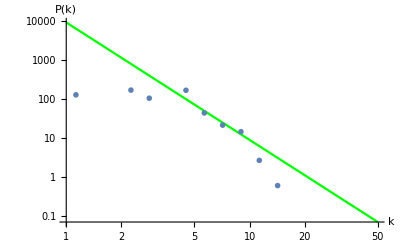

```mathematica
Show[LogLogPlot[9000x^{-3},{x,1,50},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["Out",100,15]]
```

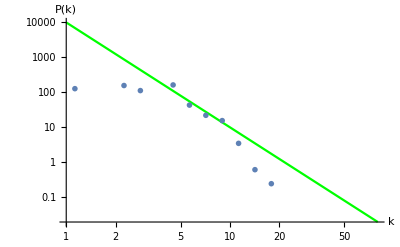

```mathematica
Show[LogLogPlot[10000x^{-3},{x,1,80},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN500["Out",150,15]]
```

```mathematica
degreeDistributionLogBinPlotN1000[mode_,g_,nbin_]:=Module[{degdata,degreeseq,h,degreedist},degdata=Import[ToString[StringForm["./Desktop/simulación/MUTACIONES/N1000/solve_nutytrans75/deg_``.dat",g]],"Table"];
Switch[mode,"In",degreeseq=degdata[[All,3]],"Out",degreeseq=degdata[[All,2]],"Total",degreeseq=degdata[[All,2]]+degdata[[All,3]]];
h=HistogramList[degreeseq,{"Log",nbin}];
degreedist=Table[{(h[[1,i]]+h[[1,i+1]])/2,h[[2,i]]/((h[[1,i+1]]-h[[1,i]]))},{i,1,Length[h[[2]]]}];
ListLogLogPlot[degreedist,PlotRange->{{10^0,10^3},{10^-3,10^4}}(*,PlotLabel->ToString[StringForm["`` degree distribution at g=``",mode,g]]*),FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,5}],None},{Table[{10^i,Superscript[10,i]},{i,-5,5}],None}},Frame->True,PlotMarkers->"OpenMarkers"]]
```

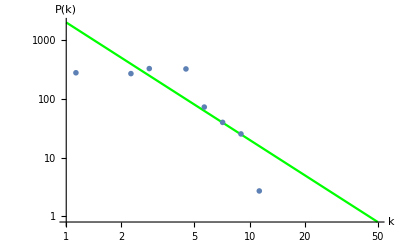

```mathematica
Show[LogLogPlot[2000x^{-2},{x,1,50},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["In",0,15]]
```

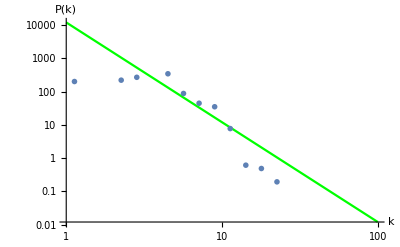

```mathematica
Show[LogLogPlot[12000x^{-3},{x,1,100},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["In",471,15]]
```

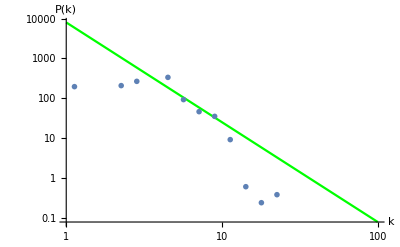

```mathematica
Show[LogLogPlot[8000x^{-2.5},{x,1,100},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["In",550,15]]
```

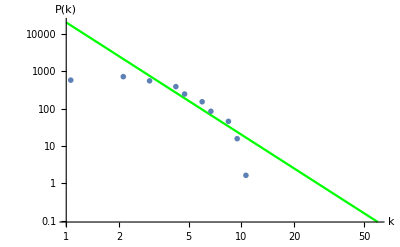

```mathematica
Show[LogLogPlot[20000x^{-3},{x,1,60},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["Out",0,15]]
```

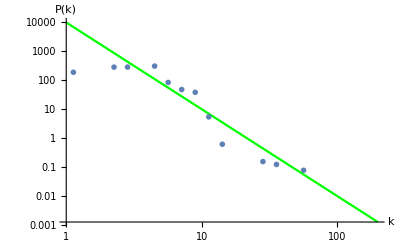

```mathematica
Show[LogLogPlot[10000x^{-3},{x,1,200},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["Out",471,15]]
```

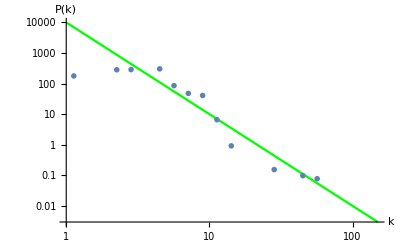

```mathematica
Show[LogLogPlot[10000x^{-3},{x,1,150},AxesLabel->{"k","P(k)"},PlotStyle->Green],degreeDistributionLogBinPlotN1000["Out",550,15]]
```